## 3D PhaseDiagram

```mathematica
Clear["Global`*"]
```

This is the full Hamiltonian having four tunable parameters. We first rescale this parameters by C, which does not change the phase diagram. Then three parameter remains, that is, Δ/C, γ/C, and Ω/C.

```mathematica
hamfull[Δ_,γ_,c_,Ω_]:=Evaluate[{{Δ-I γ,-c,Ω/2},{-c,Δ+I γ,Ω/2},{Ω/2,Ω/2,0}}];
hamfull[Δ,γ,c,Ω]//MatrixForm
Expand@Simplify[Evaluate[Simplify[Discriminant[Det[hamfull[Δ,γ,c,Ω]-e IdentityMatrix[3]],e]]]]
```

(-ⅈ γ+Δ | -c | Ω/2
-c | ⅈ γ+Δ | Ω/2
Ω/2 | Ω/2 | 0)

4 c^6-12 c^4 γ^2+12 c^2 γ^4-4 γ^6-8 c^4 Δ^2+16 c^2 γ^2 Δ^2-8 γ^4 Δ^2+4 c^2 Δ^4-4 γ^2 Δ^4+6 c^4 Ω^2-12 c^2 γ^2 Ω^2+6 γ^4 Ω^2+18 c^3 Δ Ω^2-18 c γ^2 Δ Ω^2+10 c^2 Δ^2 Ω^2-10 γ^2 Δ^2 Ω^2-2 c Δ^3 Ω^2-(15 c^2 Ω^4)/4-3 γ^2 Ω^4-9/2 c Δ Ω^4+(Δ^2 Ω^4)/4+Ω^6/2

```mathematica
ham[Δ_,Ω_,γ_]:=Evaluate[{{Δ-I γ,-1,Ω/2},{-1,Δ+I γ,Ω/2},{Ω/2,Ω/2,0}}];
ham[Δ,Ω,γ]//MatrixForm
disc[Δ_,Ω_,γ_]:=Evaluate[Discriminant[Det[ham[Δ,Ω,γ]-IdentityMatrix[3]e],e]]
Simplify[Expand[Simplify[disc[Δ,Ω,γ]]]-Expand[Simplify[disc[-Δ,Ω,γ]]]]
Collect[Det[IdentityMatrix[3]e-ham[Δ,Ω,γ]],e]
```

(-ⅈ γ+Δ | -1 | Ω/2
-1 | ⅈ γ+Δ | Ω/2
Ω/2 | Ω/2 | 0)

-Δ Ω^2 (36 γ^2+4 Δ^2+9 (-4+Ω^2))

e^3-2 e^2 Δ+Ω^2/2+(Δ Ω^2)/2+e (-1+γ^2+Δ^2-Ω^2/2)

```mathematica
Simplify[Discriminant[x^3+b x^2+c x+d,x]]
```

b^2 c^2-4 c^3-4 b^3 d+18 b c d-27 d^2

```mathematica
EP2Surf[Δ_,Ω_,γ_]:=Simplify[Discriminant[Det[ham[Δ,Ω,γ]-IdentityMatrix[3]e],e]]
EP2Surf[Δ,Ω,γ]
```

-4 γ^6+1/4 (-4-4 Δ+Ω^2)^2 (1-2 Δ+Δ^2+2 Ω^2)+γ^4 (-8 Δ^2+6 (2+Ω^2))-γ^2 (4 Δ^4+18 Δ Ω^2+3 (2+Ω^2)^2+2 Δ^2 (-8+5 Ω^2))

```mathematica
P1=Show[ContourPlot3D[Evaluate[EP2Surf[Δ,Ω,γ]]==0,{Δ,-1.5,0.5},{Ω,0,2},{γ,0,2},PlotPoints->80,ContourStyle->{RGBColor[0,.4,1,.6]},Mesh->None,PlotRange->All],Frame->True,AxesLabel->{"Δ","Ω","γ"},Boxed->True,AxesStyle->Directive[Black,14],ImageSize->300]
```

-Graphics3D-

```mathematica
(*Show[P1,Plot3D[1,{Δ,-0.5,1.5},{Ω,-1,2},Mesh->None]]*)
```

## Full phase diagram in three-level system

```mathematica
ham[Δ,Ω,γ]//MatrixForm
```

(-ⅈ γ+Δ | -1 | Ω/2
-1 | ⅈ γ+Δ | Ω/2
Ω/2 | Ω/2 | 0)

```mathematica
EP2Surf[Δ_,Ω_,γ_]:=Simplify[Discriminant[Det[ham[Δ,Ω,γ]-IdentityMatrix[3]e],e]]
EP2Surf[Δ,Ω,γ]
```

-4 γ^6+1/4 (-4-4 Δ+Ω^2)^2 (1-2 Δ+Δ^2+2 Ω^2)+γ^4 (-8 Δ^2+6 (2+Ω^2))-γ^2 (4 Δ^4+18 Δ Ω^2+3 (2+Ω^2)^2+2 Δ^2 (-8+5 Ω^2))

```mathematica
(*samere=FactorList[Resultant[ComplexExpand[Re[Det[ham[Δ,Ω,γ]-IdentityMatrix[3](er+I ei)]]],ComplexExpand[Im[Det[ham[Δ,Ω,γ]-IdentityMatrix[3](er+I ei)]]],ei]];
samere//MatrixForm
ReEqual1=Discriminant[samere[[3,1]],er]
ReEqual2=Discriminant[samere[[4,1]],er]*)
(*ReEquSurf=Show[ContourPlot3D[{ReEqual1==0,ReEqual2==0},{Δ,-0.3,1.2},{Ω,0,3},{γ,0,3},PlotPoints->80,ContourStyle->{RGBColor[1,.4,0,.6]},Mesh->None,PlotRange->All],Frame->True,AxesLabel->{"Δ","Ω","γ"}]*)
```

```mathematica
Collect[-Det[ham[Δ,Ω,γ]-IdentityMatrix[3]e],e]
a2=-Coefficient[Collect[-Det[ham[Δ,Ω,γ]-IdentityMatrix[3]e],e],e,2];
a1=Coefficient[Collect[-Det[ham[Δ,Ω,γ]-IdentityMatrix[3]e],e],e,1];
a0=-Coefficient[Collect[-Det[ham[Δ,Ω,γ]-IdentityMatrix[3]e],e],e,0];
```

e^3-2 e^2 Δ+Ω^2/2+(Δ Ω^2)/2+e (-1+γ^2+Δ^2-Ω^2/2)

```mathematica
ReEquSurf=Numerator@Simplify[(a1-3a0/a2)/2-(a2/3)^2]
```

4 Δ^3+27 Ω^2+9 Δ (-4+4 γ^2+Ω^2)

```mathematica
EP2Surf[x,y,z]
```

1/4 (-8 x^3 y^2+2 y^6-16 x^4 (-1+z^2)+24 y^2 (-1+z^2)^2-16 (-1+z^2)^3-3 y^4 (5+4 z^2)-18 x y^2 (-4+y^2+4 z^2)+x^2 (y^4-40 y^2 (-1+z^2)-32 (-1+z^2)^2))

```mathematica
P1=Show[ContourPlot3D[Evaluate[EP2Surf[Δ,Ω,γ]]==0,{Δ,-1.2,0.3},{Ω,0,3},{γ,0,3},PlotPoints->100,Mesh->None,PlotRange->All,ContourStyle->Directive[Lighter@Blue,Opacity[0.7],Lighting->"Accent"]],
Frame->True,AxesLabel->{"Δ/C","Ω/C","γ/C"},Boxed->True,AxesStyle->Directive[Black,18],ImageSize->300]
```

-Graphics3D-

```mathematica
RealSurf=ContourPlot3D[4 Δ^3+27 Ω^2+9 Δ (-4+4 γ^2+Ω^2)==0,{Δ,-1.2,0.3},{Ω,0,3},{γ,0,3},RegionFunction->Function[{x,y,z},Evaluate[EP2Surf[x,y,z]<0]],RegionBoundaryStyle->None,ContourStyle->{Lighter@Green,Opacity[0.5]},BoundaryStyle->None,Mesh->None,PerformanceGoal->"Quality",PlotPoints->100];
Show[P1,RealSurf,PlotRange->All]
```

-Graphics3D-

```mathematica
EP3EqG=FactorList[Simplify[Resultant[EP2Surf[Δ,Ω,γ],ReEquSurf,γ]]]
EP3G0=FactorList[EP2Surf[Δ,Ω,0]];
MatrixForm[EP3EqG];
EP3G0//MatrixForm;
EP3ProjLineG=EP3EqG[[2,1]]
EP3G0[[2,1]]
```

{{16,1},{16 Δ^3+27 Ω^2+27 Δ Ω^2,6}}

16 Δ^3+27 Ω^2+27 Δ Ω^2

4+4 Δ-Ω^2

```mathematica
P3=Show[ContourPlot[{EP3ProjLineG==0,EP3G0[[2,1]]==0},{Δ,-1.3,0.3},{Ω,0,3},PlotPoints->50,ContourStyle->{{RGBColor[.8,0,0,1],Thickness[0.01]},{RGBColor[0,.3,.7,1],Thickness[0.01]}}],
Graphics[{Gray,Thickness[0.01],Dashed,Line[{{0.3,0},{-1.3,0}}]}],
Graphics[{Gray,Thickness[0.01],Dashed,Line[{{0,0},{0,3.02}}]}],
Graphics[{Gray,Thickness[0.01],Dashed,Line[{{-1.01,0},{-1.01,3.02}}]}]];
```

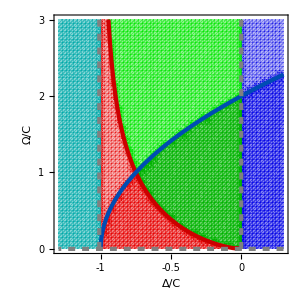

```mathematica
P4=Show[
RegionPlot[EP3G0[[2,1]]>0&&EP3ProjLineG<0&&Ω>0,{Δ,-1.3,0.3},{Ω,0,3},BoundaryStyle->None,PlotPoints->60,PlotStyle->{RGBColor[.9,0,0,.5]}],
RegionPlot[EP3G0[[2,1]]<0&&EP3ProjLineG<0&&Δ>-1,{Δ,-1.3,0.3},{Ω,0,3},BoundaryStyle->None,PlotPoints->60,PlotStyle->{RGBColor[.9,0,0,.3]}],
RegionPlot[EP3G0[[2,1]]>0&&EP3ProjLineG>0&&0<Δ<0.3,{Δ,-1.3,0.3},{Ω,0,3},BoundaryStyle->None,PlotPoints->60,PlotStyle->{RGBColor[0,0,.9,.5]}],
RegionPlot[EP3G0[[2,1]]<0&&EP3ProjLineG>0&&0<Δ<0.3,{Δ,-1.3,0.3},{Ω,0,3},BoundaryStyle->None,PlotPoints->60,PlotStyle->{RGBColor[0,0,.9,.3]}],
RegionPlot[EP3G0[[2,1]]<0&&EP3ProjLineG>0 &&Δ<0,{Δ,-1.3,0.3},{Ω,0,3},BoundaryStyle->None,PlotPoints->60,PlotStyle->{RGBColor[0,0.9,0,.45]}],
RegionPlot[EP3G0[[2,1]]>0&&EP3ProjLineG>0&&Δ<0,{Δ,-1.3,0.3},{Ω,0,3},BoundaryStyle->None,PlotPoints->60,PlotStyle->{RGBColor[0,0.7,0,.6]}],
RegionPlot[Δ<-1,{Δ,-1.3,0.3},{Ω,0,3},BoundaryStyle->None,PlotPoints->60,PlotStyle->{Darker@Cyan,Opacity[.5](*,GrayLevel[0.75]*)}],
P3,Frame->True,FrameLabel->{"Δ/C","Ω/C"},PlotTheme->"Scientific",FrameTicks->{{{0,1,2,3},None},{{-1,-0.5,0},None}},FrameStyle->Directive[Black,18,Thickness[0.0039]],PlotRange->{{-1.3,0.3},{0,3}},ImageSize->300]
```

```mathematica
(*Show[P4,ContourPlot[4 Δ^3-27 Ω^2+9 Δ (-4+4 #^2+Ω^2)==0,{Δ,-0.3,1.3},{Ω,0,3},ContourStyle->{Orange,Opacity[0.3]}]&/@Table[i,{i,0,20,0.02}]]*)
```

## 2D Ω slice cut

```mathematica
Ω0=3/5;
Ω1=2+2/5;
```

```mathematica
cs01=Flatten[Δ/.Solve[(4+4 Δ-Ω^2/.Ω->Ω0)==0,Δ]][[1]];
cs02=Flatten[Δ/.Solve[(16 Δ^3+27 Ω^2+27 Δ Ω^2/.Ω->Ω0)==0,Δ]][[1]];
cs11=Flatten[Δ/.Solve[(4+4 Δ-Ω^2/.Ω->Ω1)==0,Δ]][[1]];
cs12=Flatten[Δ/.Solve[(16 Δ^3+27 Ω^2+27 Δ Ω^2/.Ω->Ω1)==0,Δ]][[1]];
```

```mathematica
0.975-0.15
```

0.825

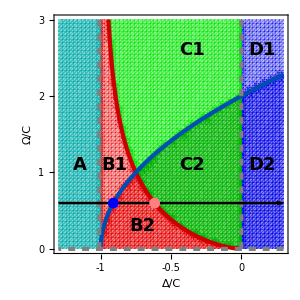

```mathematica
P5=Show[P4,With[{Ω=Ω0},Graphics[{Black,Thickness[0.006],Arrow[{{-1.3,Ω},{0.3,Ω}}]}]],(*With[{Ω=Ω1},Graphics[{Lighter@Cyan,Thickness[0.006],Arrow[{{-0.3,Ω},{1.3,Ω}}]}]],*)With[{Δ=cs01},Graphics[{Dashed,Blue,PointSize[0.025],Point[{{cs01,Ω0},{cs01,Ω0}}]}]],With[{Δ=cs02},Graphics[{Dashed,Pink,PointSize[0.025],Point[{{cs02,Ω0},{cs02,Ω0}}]}]],
Graphics[{Text[Style["C2",FontFamily->"Arial",Bold,18],{-0.35,1.1}]}],
Graphics[{Text[Style["C1",FontFamily->"Arial",Bold,18],{-0.35,2.6}]}],
Graphics[{Text[Style["B1",FontFamily->"Arial",Bold,18],{-0.9,1.1}]}],
Graphics[{Text[Style["B2",FontFamily->"Arial",Bold,18],{-0.7,0.3}]}],
Graphics[{Text[Style["A",FontFamily->"Arial",Bold,18],{-1.15,1.1}]}],
Graphics[{Text[Style["D1",FontFamily->"Arial",Bold,18],{0.15,2.6}]}],
Graphics[{Text[Style["D2",FontFamily->"Arial",Bold,18],{0.15,1.1}]}]
(*With[{Δ=cs01},Graphics[{Dashed,Blue,PointSize[0.025],Point[{{cs11,Ω1},{cs11,Ω1}}]}]],*)(*With[{Δ=cs02},Graphics[{Dashed,Pink,PointSize[0.025],Point[{{cs12,Ω1},{cs12,Ω1}}]}]]*)(*,
Graphics[{Black,PointSize[0.025],Point[{{-0.15,Ω0},{0.3,Ω0},{0.75,Ω0},{1.15,Ω0}}]}],Graphics[{Black,PointSize[0.025],Point[{{-0.15,Ω1},{0.45,Ω1},{0.968,Ω1}}]}]*)]
```

```mathematica
Export["/Users/phykai/Nutstore Files/Research/Paper_ReEntryPolariton/Paper/Figs/Fig3b.png",P5]
```

/Users/phykai/Nutstore Files/Research/Paper_ReEntryPolariton/Paper/Figs/Fig3b.png

```mathematica
compcond=Simplify[Discriminant[Det[ham[Δ,Ω0,γ]-IdentityMatrix[3]e],e]]
```

-4 γ^6+γ^4 (354/25-8 Δ^2)+((91+100 Δ)^2 (43-50 Δ+25 Δ^2))/62500+γ^2 (-10443/625-(162 Δ)/25+(62 Δ^2)/5-4 Δ^4)

```mathematica
Collect[-Det[ham[Δ,Ω,γ]-IdentityMatrix[3]e],e]
a2=-Coefficient[Collect[-Det[ham[Δ,Ω,γ]-IdentityMatrix[3]e],e],e,2];
a1=Coefficient[Collect[-Det[ham[Δ,Ω,γ]-IdentityMatrix[3]e],e],e,1];
a0=-Coefficient[Collect[-Det[ham[Δ,Ω,γ]-IdentityMatrix[3]e],e],e,0];
realcond0=(a1-3a0/a2)/2-(a2/3)^2/.{Ω->Ω0}
realcond1=(a1-3a0/a2)/2-(a2/3)^2/.{Ω->Ω1}
```

e^3-2 e^2 Δ+Ω^2/2+(Δ Ω^2)/2+e (-1+γ^2+Δ^2-Ω^2/2)

-(4 Δ^2)/9+1/2 (-59/50+γ^2-(3 (-9/50-(9 Δ)/50))/(2 Δ)+Δ^2)

-(4 Δ^2)/9+1/2 (-97/25+γ^2-(3 (-72/25-(72 Δ)/25))/(2 Δ)+Δ^2)

```mathematica
gs=γ/.Solve[(-(4 Δ^2)/9+1/2 (-59/25+γ^2-(3 (-72/25-(72 Δ)/25))/(2 Δ)+Δ^2)/.{Δ->cs02})==0,γ][[2]]
```

(√(-972-99 Root-0.616Root[243+243 #1+400 #1^3&,1]-0.6157336413227936-25 (Root-0.616Root[243+243 #1+400 #1^3&,1]-0.6157336413227936)^3))/(15 √(Root-0.616Root[243+243 #1+400 #1^3&,1]-0.6157336413227936))

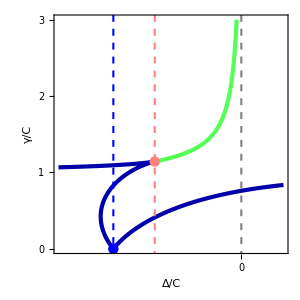

Export::nodir: Directory C:\Users\phykai\Nutstore Files\Research\Paper_ReEntryPolariton\Paper\Figs\ does not exist.

Export::noopen: Cannot open /Users/phykai/Nutstore Files/Research/Paper_ReEntryPolariton/Paper/Figs/Fig3c.png.

$Failed

```mathematica
P6=Show[ContourPlot[compcond==0,{Δ,-1.3,0.3},{γ,0,3},PlotPoints->100,ContourStyle->Directive[Darker@Blue,Opacity[1],(*Black*),Thickness[0.01]]],
ContourPlot[realcond0==0,{Δ,0,cs02},{γ,0,3},PlotPoints->100,ContourStyle->Directive[Lighter@Green,Opacity[1],(*Black,Dashed,*)Thickness[0.01]]],
Graphics[{Dashed,Thickness[0.005],Gray,Line[{{0,-0.3},{0,3.3}}],Line[{{1,-0.3},{1,3.3}}]}],
With[{Δ=cs01},Graphics[{Dashed,Blue,PointSize[0.025],Point[{{cs01,0}}]}]],
Graphics[{Blue,Dashed,Thickness[0.005],Line[{{cs01,-0.3},{cs01,3.3}}]}],With[{Δ=cs02},Graphics[{Dashed,Pink,PointSize[0.025],Point[{{cs02,N[gs]}}]}]],Graphics[{Pink,Dashed,Thickness[0.005],Line[{{cs02,-0.3},{cs02,3.3}}]}],
Frame->True,PlotTheme->"Scientific",FrameTicks->{{{0,1,2,3},None},{{0,0.5,1},None}},FrameStyle->Directive[Black,18,Thickness[0.0039]],PlotRange->{{-1.3,0.3},{0,3}},ImageSize->300,FrameLabel->{"Δ/C","γ/C"}]
Export["/Users/phykai/Nutstore Files/Research/Paper_ReEntryPolariton/Paper/Figs/Fig3c.png",P6]
```

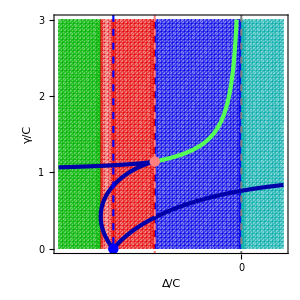

Export::nodir: Directory C:\Users\phykai\Nutstore Files\Research\Paper_ReEntryPolariton\Paper\Figs\ does not exist.

Export::noopen: Cannot open /Users/phykai/Nutstore Files/Research/Paper_ReEntryPolariton/Paper/Figs/Fig3cv1.png.

$Failed

```mathematica
P7=Show[RegionPlot[Δ<-1,{Δ,-1.3,0.3},{Ω,0,3},BoundaryStyle->None,PlotPoints->60,PlotStyle->{RGBColor[0,0.7,0,.6]}],RegionPlot[cs02<Δ<0,{Δ,-1.3,0.3},{Ω,0,3},BoundaryStyle->None,PlotPoints->60,PlotStyle->{RGBColor[0,0,.9,.5]}],RegionPlot[cs01<Δ<cs02,{Δ,-1.3,0.3},{Ω,0,3},BoundaryStyle->None,PlotPoints->60,PlotStyle->{RGBColor[.9,0,0,.5]}],RegionPlot[-1<Δ<cs01,{Δ,-1.3,0.3},{Ω,0,3},BoundaryStyle->None,PlotPoints->60,PlotStyle->{RGBColor[.9,0,0,.3]}],RegionPlot[0<Δ<0.3,{Δ,-1.3,0.3},{Ω,0,3},BoundaryStyle->None,PlotPoints->60,PlotStyle->{Darker@Cyan,Opacity[.5]}],P6,Frame->True,PlotTheme->"Scientific",FrameTicks->{{{0,1,2,3},None},{{0,0.5,1},None}},FrameStyle->Directive[Black,18,Thickness[0.0039]],PlotRange->{{-1.3,0.3},{0,3}},ImageSize->300,FrameLabel->{"Δ/C","γ/C"}]
Export["/Users/phykai/Nutstore Files/Research/Paper_ReEntryPolariton/Paper/Figs/Fig3cv1.png",P7]
```

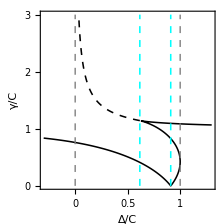
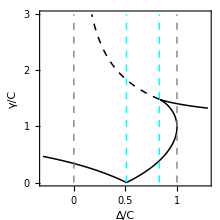
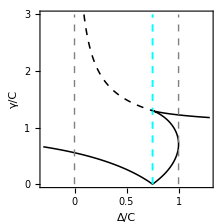
Ω0=3/5;7/5;1. 
-Graphics--Graphics--Graphics-

## Eigenvalues in different regions

```mathematica
Clear["Global`*"]
```

```mathematica
R0=3/5;
ham[δ_,R0_,G_]:={{δ+I G,R0,C0},{R0,0,R0},{C0,R0,δ-I G}};
ham[δ,R0,G]//MatrixForm
```

(ⅈ G+δ | 3/5 | C0
3/5 | 0 | 3/5
C0 | 3/5 | -ⅈ G+δ)

```mathematica
compcond=Simplify[Discriminant[Det[ham[δ,R0,G]-IdentityMatrix[3]e],e]]
```

4 C0^6-4 G^6-(648 C0^3 δ)/25+G^4 (216/25-8 δ^2)+C0^4 (216/25-12 G^2-8 δ^2)+(324 (72+25 δ^2))/15625+72/625 C0 δ (81+225 G^2+25 δ^2)-4/625 G^2 (972+2250 δ^2+625 δ^4)+4/125 C0^2 (-243+375 G^4+450 δ^2+125 δ^4+20 G^2 (-27+25 δ^2))

```mathematica
Collect[-Det[ham[δ,R0,G]-IdentityMatrix[3]e],e]
a2=-Coefficient[Collect[-Det[ham[δ,R0,G]-IdentityMatrix[3]e],e],e,2];
a1=Coefficient[Collect[-Det[ham[δ,R0,G]-IdentityMatrix[3]e],e],e,1];
a0=-Coefficient[Collect[-Det[ham[δ,R0,G]-IdentityMatrix[3]e],e],e,0];
```

-(18 C0)/25+e^3+(18 δ)/25-2 e^2 δ+e (-18/25-C0^2+G^2+δ^2)

```mathematica
realcond=(a1-3a0/a2)/2-(a2/3)^2;
```

```mathematica
engeq=With[{δ0=1/2},(Det[ham[δ,R0,G]-IdentityMatrix[3]e]/.Solve[Evaluate[realcond/.{δ->δ0}]==0,G∈Reals][[2]])/.{δ->δ0}]
Solve[engeq==0,e]//N
```

Part::partw: Part 2 of {} does not exist.

ReplaceAll::reps: {{}⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

-9/25+(18 C0)/25+(47 e)/100+C0^2 e+e^2-e^3-e G^2/.{}⟦2⟧

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{e→0.333333-(0.00419974 (-24100.-30000. C0^2+30000. G^2))/(-3.49×10^6+1.944×10^7 C0+9.×10^6 C0^2-9.×10^6 G^2+√(4. (-24100.-30000. C0^2+30000. G^2)^3+(-3.49×10^6+1.944×10^7 C0+9.×10^6 C0^2-9.×10^6 G^2-2.7×10^7 InverseFunction[ReplaceAll,1,2][0.,{}⟦2⟧])^2)-2.7×10^7 InverseFunction[ReplaceAll,1,2][0.,{}⟦2⟧])^(1/3)+0.00264567 (-3.49×10^6+1.944×10^7 C0+9.×10^6 C0^2-9.×10^6 G^2+√(4. (-24100.-30000. C0^2+30000. G^2)^3+(-3.49×10^6+1.944×10^7 C0+9.×10^6 C0^2-9.×10^6 G^2-2.7×10^7 InverseFunction[ReplaceAll,1,2][0.,{}⟦2⟧])^2)-2.7×10^7 InverseFunction[ReplaceAll,1,2][0.,{}⟦2⟧])^(1/3)},{e→0.333333+((0.00209987+0.00363708 ⅈ) (-24100.-30000. C0^2+30000. G^2))/(-3.49×10^6+1.944×10^7 C0+9.×10^6 C0^2-9.×10^6 G^2+√(4. (-24100.-30000. C0^2+30000. G^2)^3+(-3.49×10^6+1.944×10^7 C0+9.×10^6 C0^2-9.×10^6 G^2-2.7×10^7 InverseFunction[ReplaceAll,1,2][0.,{}⟦2⟧])^2)-2.7×10^7 InverseFunction[ReplaceAll,1,2][0.,{}⟦2⟧])^(1/3)-(0.00132283-0.00229122 ⅈ) (-3.49×10^6+1.944×10^7 C0+9.×10^6 C0^2-9.×10^6 G^2+√(4. (-24100.-30000. C0^2+30000. G^2)^3+(-3.49×10^6+1.944×10^7 C0+9.×10^6 C0^2-9.×10^6 G^2-2.7×10^7 InverseFunction[ReplaceAll,1,2][0.,{}⟦2⟧])^2)-2.7×10^7 InverseFunction[ReplaceAll,1,2][0.,{}⟦2⟧])^(1/3)},{e→0.333333+((0.00209987-0.00363708 ⅈ) (-24100.-30000. C0^2+30000. G^2))/(-3.49×10^6+1.944×10^7 C0+9.×10^6 C0^2-9.×10^6 G^2+√(4. (-24100.-30000. C0^2+30000. G^2)^3+(-3.49×10^6+1.944×10^7 C0+9.×10^6 C0^2-9.×10^6 G^2-2.7×10^7 InverseFunction[ReplaceAll,1,2][0.,{}⟦2⟧])^2)-2.7×10^7 InverseFunction[ReplaceAll,1,2][0.,{}⟦2⟧])^(1/3)-(0.00132283+0.00229122 ⅈ) (-3.49×10^6+1.944×10^7 C0+9.×10^6 C0^2-9.×10^6 G^2+√(4. (-24100.-30000. C0^2+30000. G^2)^3+(-3.49×10^6+1.944×10^7 C0+9.×10^6 C0^2-9.×10^6 G^2-2.7×10^7 InverseFunction[ReplaceAll,1,2][0.,{}⟦2⟧])^2)-2.7×10^7 InverseFunction[ReplaceAll,1,2][0.,{}⟦2⟧])^(1/3)}}

```mathematica
Gc=(DeleteDuplicates[G/.Solve[{Numerator[Resultant[realcond,compcond,δ]]==0,G∈Reals,G>0},G]][[1]])
δc=(δ/.Solve[{Evaluate[realcond/.{G->Gc}]==0,δ∈Reals,δ>0},δ])[[1]]
e/.Solve[Det[ham[δc,R0,Gc]-e IdentityMatrix[3]]==0,e]//N
```

DeleteDuplicates::normal: Nonatomic expression expected at position 1 in DeleteDuplicates[G].

G

Part::partd: Part specification δ⟦1⟧ is longer than depth of object.

δ⟦1⟧

{0.666667 δ⟦1⟧+(0.419974 (-2.16-3. C0^2+3. G^2-1. δ⟦1⟧^2))/((-19.44 C0+6.48 δ⟦1⟧-18. C0^2 δ⟦1⟧+18. G^2 δ⟦1⟧+2. δ⟦1⟧^3+√(4. (-2.16-3. C0^2+3. G^2-1. δ⟦1⟧^2)^3+(-19.44 C0+6.48 δ⟦1⟧-18. C0^2 δ⟦1⟧+18. G^2 δ⟦1⟧+2. δ⟦1⟧^3)^2))^(1/3))-0.264567 (-19.44 C0+6.48 δ⟦1⟧-18. C0^2 δ⟦1⟧+18. G^2 δ⟦1⟧+2. δ⟦1⟧^3+√(4. (-2.16-3. C0^2+3. G^2-1. δ⟦1⟧^2)^3+(-19.44 C0+6.48 δ⟦1⟧-18. C0^2 δ⟦1⟧+18. G^2 δ⟦1⟧+2. δ⟦1⟧^3)^2))^(1/3),0.666667 δ⟦1⟧-((0.209987+0.363708 ⅈ) (-2.16-3. C0^2+3. G^2-1. δ⟦1⟧^2))/((-19.44 C0+6.48 δ⟦1⟧-18. C0^2 δ⟦1⟧+18. G^2 δ⟦1⟧+2. δ⟦1⟧^3+√(4. (-2.16-3. C0^2+3. G^2-1. δ⟦1⟧^2)^3+(-19.44 C0+6.48 δ⟦1⟧-18. C0^2 δ⟦1⟧+18. G^2 δ⟦1⟧+2. δ⟦1⟧^3)^2))^(1/3))+(0.132283-0.229122 ⅈ) (-19.44 C0+6.48 δ⟦1⟧-18. C0^2 δ⟦1⟧+18. G^2 δ⟦1⟧+2. δ⟦1⟧^3+√(4. (-2.16-3. C0^2+3. G^2-1. δ⟦1⟧^2)^3+(-19.44 C0+6.48 δ⟦1⟧-18. C0^2 δ⟦1⟧+18. G^2 δ⟦1⟧+2. δ⟦1⟧^3)^2))^(1/3),0.666667 δ⟦1⟧-((0.209987-0.363708 ⅈ) (-2.16-3. C0^2+3. G^2-1. δ⟦1⟧^2))/((-19.44 C0+6.48 δ⟦1⟧-18. C0^2 δ⟦1⟧+18. G^2 δ⟦1⟧+2. δ⟦1⟧^3+√(4. (-2.16-3. C0^2+3. G^2-1. δ⟦1⟧^2)^3+(-19.44 C0+6.48 δ⟦1⟧-18. C0^2 δ⟦1⟧+18. G^2 δ⟦1⟧+2. δ⟦1⟧^3)^2))^(1/3))+(0.132283+0.229122 ⅈ) (-19.44 C0+6.48 δ⟦1⟧-18. C0^2 δ⟦1⟧+18. G^2 δ⟦1⟧+2. δ⟦1⟧^3+√(4. (-2.16-3. C0^2+3. G^2-1. δ⟦1⟧^2)^3+(-19.44 C0+6.48 δ⟦1⟧-18. C0^2 δ⟦1⟧+18. G^2 δ⟦1⟧+2. δ⟦1⟧^3)^2))^(1/3)}

```mathematica
Show[ContourPlot[compcond==0,{δ,0,2},{G,0,3},PlotPoints->100,ContourStyle->Directive[Black,Thickness[0.005]]],ContourPlot[realcond==0,{δ,0,δc},{G,0,3},PlotPoints->100,ContourStyle->Directive[Black,Dashed,Thickness[0.005]]],Graphics[{Red,PointSize[0.02],Opacity[0.7],Point[N@{δc,Gc}]}],Frame->True,FrameStyle->Directive[Black,16],FrameLabel->{"δ","G"}]
```

Part::partd: Part specification δ⟦1⟧ is longer than depth of object.

ContourPlot::plln: Limiting value δ⟦1⟧ in {δ,0,δ⟦1⟧} is not a machine-sized real number.

Show::gcomb: Could not combine the graphics objects in Show[,ContourPlot[realcond==0,{δ,0,δc},{G,0,3},PlotPoints→100,ContourStyle→Directive[Black,Dashed,Thickness[0.005]]],,Frame→True,FrameStyle→Directive[color,16],FrameLabel→{δ,G}].

Show[-Graphics-,ContourPlot[realcond==0,{δ,0,δc},{G,0,3},PlotPoints→100,ContourStyle→Directive[Black,Dashed,Thickness[0.005]]],-Graphics-,Frame→True,FrameStyle→Directive[GrayLevel[0],16],FrameLabel→{δ,G}]

```mathematica
δ=δc+0.1
R0=R0
G=0.9
```

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of δ⟦1⟧.

Hold[0.1+δ⟦1⟧]

3/5

0.9

```mathematica
Plot[{Evaluate[Re[Eigenvalues[ham[δ,3/5,8/10]]]]},{δ,0,1.5},PlotStyle->{{Thickness[0.008]}},PlotRange->All,Frame->True,FrameStyle->Directive[Black,16],FrameLabel->{"G","ReE"}]
Plot[{Evaluate[Im[Eigenvalues[ham[δ,3/5,8/10]]]]},{δ,0,1.5},PlotStyle->{{Thickness[0.008]}},PlotRange->All,Frame->True,FrameStyle->Directive[Black,16],FrameLabel->{"G","ReE"}]
```

-Graphics-

-Graphics-

```mathematica
F1=With[{δ=δc+0.2,R0=R0},Plot[{Evaluate[Re[Eigenvalues[ham[δ,R0,G]]]]},{G,0,3},PlotStyle->{Thickness[0.008]},PlotRange->All,Frame->True,FrameStyle->Directive[Black,16],FrameLabel->{"G","ReE"}]]
F2=With[{δ=δc+0.205,R0=R0},Plot[{Evaluate[Im[Eigenvalues[ham[δ,R0,G]]]]},{G,0,3},PlotStyle->{Thickness[0.008]},PlotRange->All,Frame->True,FrameStyle->Directive[Black,16],FrameLabel->{"G","ImE"}]]
```

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of δ⟦1⟧.

General::stop: Further output of $RecursionLimit::reclim2 will be suppressed during this calculation.

Root::npoly: Hold[-90 C0+90 (δ⟦1⟧+0.2)+(-18-25 C0^2+25 G^2+25 (Part[«2»]+0.2)^2) #1-10 (δ⟦1⟧+0.2) #1^2+#1^3] is not a polynomial in #1.

General::stop: Further output of Root::npoly will be suppressed during this calculation.

-Graphics-

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of δ⟦1⟧.

General::stop: Further output of $RecursionLimit::reclim2 will be suppressed during this calculation.

Root::npoly: Hold[-90 C0+90 (δ⟦1⟧+0.205)+(-18-25 C0^2+25 G^2+25 (Part[«2»]+0.205)^2) #1-10 (δ⟦1⟧+0.205) #1^2+#1^3] is not a polynomial in #1.

General::stop: Further output of Root::npoly will be suppressed during this calculation.

-Graphics-

The eigenspace at EP-3 collapse into one dimension.

```mathematica
N[Eigensystem@ham[δc,R0,Gc]]//MatrixForm
Solve[Discriminant[Det[ham[δ,R0,0]-e IdentityMatrix[3]],e]==0,δ∈Reals]//N
```

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of δ⟦1⟧.

Hold[N[Eigensystem[ham[δc,R0,Gc]]]]

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of δ⟦1⟧.

Hold[N[Solve[Discriminant[Det[ham[δ,R0,0]-e IdentityMatrix[3]],e]==0,δ∈ℝ]]]